# This script accompanies the paper Pólya’s conjecture for Dirichlet eigenvalues of annuli

## Computer-assisted part can be found towards the end of the notebook, see §8

(c) N. Filonov, M. Levitin, I. Polterovich, and D. A. Sher, 2025

For questions and comments, e-mail M.Levitin@reading.ac.uk

## Preliminaries

```mathematica
curdir=SetDirectory[NotebookDirectory[]];
SaveDir="./";
```

MaTeX

```mathematica
<<MaTeX`
texStyle={};
SetOptions[MaTeX,"BasePreamble"->{"\\usepackage{amsmath,amssymb,xcolor}","\\usepackage{fourier}","\\usepackage{ebgaramond}"},FontSize->12,Magnification->1];
```

cleanContourPlot from https://mathematica.stackexchange.com/questions/3190/saner-alternative-to-contourplot-fill

```mathematica
cleanContourPlot[cp_Graphics]:=Module[{points,groups,regions,lines},groups=Cases[cp,{style__,g_GraphicsGroup}:>{{style},g},Infinity];
points=First@Cases[cp,GraphicsComplex[pts_,___]:>pts,Infinity];
regions=Table[Module[{group,style,polys,edges,cover,graph},{style,group}=g;
polys=Join@@Cases[group,Polygon[pt_,___]:>pt,Infinity];
edges=Join@@(Partition[#,2,1,1]&/@polys);
cover=Cases[Tally[Sort/@edges],{e_,1}:>e];
graph=Graph[UndirectedEdge@@@cover];
{Sequence@@style,FilledCurve[List/@Line/@First/@Map[First,FindEulerianCycle/@(Subgraph[graph,#]&)/@ConnectedComponents[graph],{3}]]}],{g,groups}];
lines=Cases[cp,_Tooltip,Infinity];
Graphics[GraphicsComplex[points,{regions,lines}],Sequence@@Options[cp]]]
```

Colours and lines

```mathematica
clrs={ Pink, Blue, Orange,Darker[Green], Darker[Yellow]};
mydashing0=Charting`ResolvePlotTheme["Monochrome",Plot][[7]][[2]][[5]][[2]];
mydashing=Table[Directive[mydashing0[[j,2]], mydashing0[[j,4]]],{j,1,8}];
```

## §1. Introduction and main result

Figures 1 and 2 are towards the end of the notebook

## §2. Regions I and II via isoperimetric inequalities and comparison with flat cylinders

Figure 3

```mathematica
h[r_] := (1-r); rf = 1/2;
f31a=Show[ParametricPlot3D[{ρ Cos[ψ],ρ Sin[ψ],1-h[rf]},{ψ,0,2Pi},{ρ,rf,1},Axes->False,Boxed->False,PlotStyle->Lighter[Lighter[Blue]], Mesh->None,PlotRange->{{-1,1},{-1,1},{0,1}}],
ParametricPlot3D[{Cos[ψ],Sin[ψ],1-h[rf]},{ψ,0,2Pi}, PlotStyle->Directive[Black,Thick]],
ParametricPlot3D[{rf Cos[ψ],rf Sin[ψ],1-h[rf]},{ψ,0,2Pi}, PlotStyle->Directive[Black,Thick]],
Graphics3D[{Black, Line[{{0,0,1-h[rf]},{rf,0,1-h[rf]}}],Inset[MaTeX["r"], {rf/2,0,1-h[rf]}, Scaled[{1/2,0}]]
}],
ParametricPlot3D[{Cos[ψ],Sin[ψ],z},{ψ,0,2Pi},{z,1-h[rf],1}, Axes->False,Boxed->False,AxesOrigin->{0,0,0},PlotStyle->{Opacity[0]},MeshStyle->None,Ticks->None,PlotRange->{{-1,1},{-1,1},{0,1}}],
Method->{"ShrinkWrap"->True},ImageSize->240, PlotRange->Full
];
f32a=Show[ParametricPlot3D[{Cos[ψ],Sin[ψ],z},{ψ,0,2Pi},{z,1-h[rf],1}, Axes->False,Boxed->False,AxesOrigin->{0,0,0}, PlotTheme->"ZMesh", PlotStyle->LightBlue,Ticks->None,PlotRange->{{-1,1},{-1,1},{0,1}}], 
ParametricPlot3D[{Cos[ψ],Sin[ψ],1},{ψ,0,2Pi}, PlotStyle->Directive[Black,Thick]],
ParametricPlot3D[{Cos[ψ],Sin[ψ],1-h[rf]},{ψ,0,2Pi}, PlotStyle->Directive[Black,Thick]],
Graphics3D[{Black, {Dashed, Line[{{0,0,1},{0,0,1-h[rf]}}]},
Line[{{0,0,1-h[rf]},{0,1,1-h[rf]}}],
Inset[MaTeX["1-r"], {0,0,1-h[rf]/2},Scaled[{1.1,0}]],
Inset[MaTeX["1"], {0,2/3,1-h[rf]},Scaled[{1/2,1.1}]]
}],Method->{"ShrinkWrap"->True},ImageSize->240, PlotRange->Full
];
anncyla=GraphicsRow[{f31a,f32a}]
```

-Graphics-

```mathematica
Export[SaveDir<>"fig-anncyl-alt.pdf", anncyla];
```

Theorem 2.1

```mathematica
Subscript[η, I][r_]:=Sqrt[8/(1-r^2)];
Subscript[ζ, I][λ_]:=Piecewise[{{0,λ<=Sqrt[8]},{Sqrt[λ^2-8], λ>Sqrt[8]}}];
```

Theorem 2.3

Statement and Figure 4

```mathematica
rj=<|0->0, 1->2/3, 2->4/5, 3->17/20, 4->22/25,5->1|>;
ηIIj[j_, r_]:=(j+1) Sqrt[r]Pi/(1-r);
```

```mathematica
Subscript[η, II][r_]:=Piecewise[Table[{ηIIj[j, r],rj[j]<=r<rj[j+1]}, {j,0,4}]];
```

```mathematica
λrjp = Join[Table[{rj[j], ηIIj[j-1,rj[j]]}, {j,1,4}],
Table[{rj[j], ηIIj[j,rj[j]]}, {j,1,4}]]
```

{{2/3,√6 π},{4/5,4 √5 π},{17/20,2 √85 π},{22/25,(20 √22 π)/3},{2/3,2 √6 π},{4/5,6 √5 π},{17/20,(8 √85 π)/3},{22/25,(25 √22 π)/3}}

```mathematica
figetaII=Plot[Subscript[η, II][r], {r,0,1},Exclusions->None,PlotRange->{-35,200}, PlotStyle->clrs[[2]],Epilog->{Red,PointSize[Medium],Point[λrjp],Black, Thin,Table[Line[{{rj[j],0},{rj[j], If[j<5,If[j==1 || j==3, 1.5 Subscript[η, II][rj[j]]+30, Subscript[η, II][rj[j]]],200]}}],{j,1,5}],
Table[Inset[MaTeX[rj[j]], {rj[j],If[j==1 || j==3,1.5 Subscript[η, II][rj[j]]+30,0]},Scaled[{0.5,If[j==1 || j==3,0,1]}]],{j,1,5}]},Ticks->{None,{50,100,150,200}},AxesLabel->MaTeX[{"r", "\\eta_{\\mathrm{II}}(r)"}]];
```

```mathematica
Subscript[ζ, II][λ_]:=Piecewise[Flatten[
Table[
If[i<5, 
{{λ-i Pi/(2λ)(Sqrt[4λ^2+i^2Pi^2]-i Pi),  i Pi Sqrt[rj[i-1]]/(1-rj[i-1])<=λ<i Pi Sqrt[rj[i]]/(1-rj[i])}, {rj[i]λ,i Pi Sqrt[rj[i]]/(1-rj[i])<=λ<(i+1) Pi Sqrt[rj[i]]/(1-rj[i])}},
{{λ-i Pi/(2λ)(Sqrt[4λ^2+i^2Pi^2]-i Pi),  i Pi Sqrt[rj[i-1]]/(1-rj[i-1])<=λ}}], 
{i,1,5}],
1]
];
```

```mathematica
figzetaII=Plot[Subscript[ζ, II][λ],{λ,0,160}, PlotRange->{-35,160},PlotStyle->clrs[[2]],Epilog->{Red, PointSize[Medium],Point[Table[{j Pi Sqrt[rj[j]]/(1-rj[j]),Subscript[ζ, II][j Pi Sqrt[rj[j]]/(1-rj[j])]},{j,1,4}]],
Point[Table[{j Pi Sqrt[rj[j-1]]/(1-rj[j-1]),Subscript[ζ, II][j Pi Sqrt[rj[j-1]]/(1-rj[j-1])]},{j,2,5}]],
Black, Thin,
Table[Line[{{j Pi Sqrt[rj[j]]/(1-rj[j]),0},{j Pi Sqrt[rj[j]]/(1-rj[j]),1.2 (Subscript[ζ, II][j Pi Sqrt[rj[j]]/(1-rj[j])]+10)}}], {j,1,4}],
Table[Line[{{j Pi Sqrt[rj[j-1]]/(1-rj[j-1]),0},{j Pi Sqrt[rj[j-1]]/(1-rj[j-1]),Subscript[ζ, II][j Pi Sqrt[rj[j-1]]/(1-rj[j-1])]}}], {j,2,5}],
Table[Inset[MaTeX[j Pi Sqrt[rj[j]]/(1-rj[j])],{j Pi Sqrt[rj[j]]/(1-rj[j]),1.2 (Subscript[ζ, II][j Pi Sqrt[rj[j]]/(1-rj[j])]+10)}, Scaled[{0.5,0}]],{j,1,4}],
Table[Inset[MaTeX[j Pi Sqrt[rj[j-1]]/(1-rj[j-1])],{j Pi Sqrt[rj[j-1]]/(1-rj[j-1]),0}, Scaled[{0.5,1}]],{j,2,5}]
}, 
AxesLabel->MaTeX[{"\\lambda", "\\zeta_{\\mathrm{II}}(\\lambda)"}],Ticks->{None,{50,100,150}}];
```

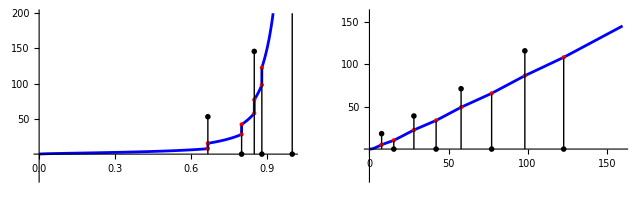

```mathematica
figetazetaII=GraphicsRow[{figetaII,figzetaII}]
Export[SaveDir<>"figetazetaII.pdf",figetazetaII];
```

Proof and Figure 5

```mathematica
S[j_,τ_,r_]:=Sum[-4 (1-r^2)-16/τ[[n]]+n^2 π^2 r (1+r)^2 τ[[n]], {n,1,j}]
```

```mathematica
S[1,{1},r]
S[2,{Subscript[τ, 1],1-Subscript[τ, 1]},r]//Simplify
S[3,{Subscript[τ, 1],Subscript[τ, 2],1-Subscript[τ, 1]-Subscript[τ, 2]},r]//Simplify
```

-16+π^2 r (1+r)^2-4 (1-r^2)

4 (-2+2 r^2+π^2 r (1+r)^2+4/(-1+τ_1))-16/τ_1-3 π^2 r (1+r)^2 τ_1

12 (-1+r^2)-16/τ_1+π^2 r (1+r)^2 τ_1-16/τ_2+4 π^2 r (1+r)^2 τ_2+16/(-1+τ_1+τ_2)-9 π^2 r (1+r)^2 (-1+τ_1+τ_2)

Case j=1

```mathematica
S[1,{1},2/3]//Simplify
%//N
```

2/27 (-246+25 π^2)

0.054823

Case j=2

```mathematica
xt={1/4,3/8,1/2};
xtt=MaTeX[{"\\frac{1}{4}", "\\frac{3}{8}","\\frac{1}{2}"}];
yt={0.80,0.85};
```

```mathematica
rstar=Simplify[SolveValues[S[2,{Subscript[τ, 1],1-Subscript[τ, 1]},r]==0 && r>0 && 0<Subscript[τ, 1]<1, r], 0<Subscript[τ, 1]<1][[1]]
```

Root[-16-8 τ_1+8 τ_1^2+#1 (4 π^2 τ_1-7 π^2 τ_1^2+3 π^2 τ_1^3)+#1^3 (4 π^2 τ_1-7 π^2 τ_1^2+3 π^2 τ_1^3)+#1^2 (8 τ_1+8 π^2 τ_1-8 τ_1^2-14 π^2 τ_1^2+6 π^2 τ_1^3)&,1]

```mathematica
figrstar2=Plot[rstar, {Subscript[τ, 1],0.2,0.5}, AxesOrigin->{0.2,0.76}, PlotStyle->{Thick, Blue},AxesLabel->MaTeX[{"\\tau_1", "r_2^*((\\tau_1,1-\\tau_1))"}],Ticks->{{xt, xtt}//Transpose,{yt, MaTeX[yt]}//Transpose}, Epilog->{Inset[●,{3/8,0.76},{Center,Center}]},ImageSize->72 4];
```

```mathematica
S[2,{3/8,5/8},4/5]//Simplify
%//N
```

23/750 (-2320+243 π^2)

2.40163

Case j=3

```mathematica
xyt={1/8,1/4,3/8, 1/2};
xytt=MaTeX[{"\\frac{1}{8}","\\frac{1}{4}", "\\frac{3}{8}","\\frac{1}{2}"}];
```

```mathematica
figrstar3=ContourPlot[SolveValues[S[3,{Subscript[τ, 1],Subscript[τ, 2],1-Subscript[τ, 1]-Subscript[τ, 2]},r]==0 && r>0, r][[1]], {Subscript[τ, 1],0.1,0.4}, {Subscript[τ, 2],0.1,0.6},ContourLabels-> Function[{x,y,z},Text[Framed[z,Background->White],{x,y}]], Contours->{0.85,.9, 0.95},ContourStyle->Black,Frame->False,Axes->True, PlotTheme->"Scientific",Ticks->{{xyt,xytt}//Transpose,{xyt,xytt}//Transpose},AxesLabel->MaTeX[{"\\tau_1", "\\tau_2"}],Epilog->{Inset[●,{1/4,1/4},{Center,Center}]},ImageSize->60 4];
figrstar31=Show[cleanContourPlot[figrstar3], Graphics[{White, Text[0.85,{0.23,0.325}],Text[0.9,{0.375,0.25}],Text[0.95,{0.18,0.525}]}]];
```

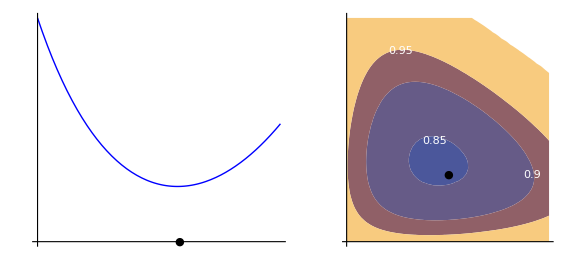

```mathematica
figrstar23=GraphicsRow[{figrstar2,figrstar31}]
Export[SaveDir<>"figrstar23.pdf",figrstar23];
```

```mathematica
S[3,{1/4,1/4,1/2},17/20]//Simplify
%//N
```

(-5226560+535279 π^2)/32000

1.7635

Case j=4

```mathematica
S[4,{1/6,1/6,1/5,7/15},22/25]//Together
%//N
```

(-169474000+17179393 π^2)/546875

0.145943

## §5. Bounds on the phase functions difference and reduction to a lattice counting problem

```mathematica
G[λ_,z_]:=(√(λ^2-z^2)-z ArcCos[z/λ])/π;
H[λ_,z_]:= (3λ^2+2z^2)/(24Pi(λ^2-z^2)^(3/2));
H1[λ_,z_]:= (3λ^2+2λ^2)/(24Pi(λ^2-z^2)^(3/2));
F[λ_,z_]:=If[z<λ,Max[G[λ,z]-H[λ,z],-1/4],-1/4];
Φ[λ_,μ_,z_]:=G[λ,z]-G[μ,z];
```

Figure 6

```mathematica
λ0=20; μ0=12; 
interse=NSolveValues[{G[μ0,z]-H[ μ0,z]+1/4==0, μ0/2<=z<= μ0}, z][[1]];
interse1=NSolveValues[{G[μ0-1,z]-H[ μ0-1,z]+1/4==0, μ0/2-1/2<=z<= μ0}, z][[1]];
{x0, y0}={interse, G[λ0,interse]+1/4}; r0=7/12;
zoom=Function[{x,y}, (x-x0)^2+(y-y0)^2<=r0^2];
```

```mathematica
figboundsGFH1=Show[
Plot[G[ λ0,z]-G[μ0,z]+H[ μ0,z],{z,0, interse}, PlotStyle->Blue],
Plot[G[ λ0,z]-G[μ0,z]+H[ μ0,z],{z,interse, μ0}, PlotStyle->{Dashed,Blue}],
Plot[G[ λ0,z]+1/4,{z,0, interse}, PlotStyle->{Dashed, Orange}],
Plot[G[ λ0,z]+1/4,{z,interse, λ0}, PlotStyle->Orange],
Plot[Φ[λ0,μ0,z]+1/4,{z,0,μ0},PlotStyle->{Magenta, mydashing[[4]]}],
PlotRange->{{0,λ0},{0,3}}, AxesOrigin->{0,0},Epilog->{Dotted, Black,Line[{{μ0,0},{μ0,3}}],Inset[MaTeX["\\textcolor{blue}{\\Phi_{\\lambda,\\mu}(z)+H_\\mu(z)}"],{2μ0/5,2.1}],
Inset[MaTeX["\\textcolor{magenta}{\\Phi_{\\lambda,\\mu}(z)+\\frac{1}{4}}"],{2μ0/5,2.9}],Inset[MaTeX["\\textcolor{orange}{G_\\lambda(z)+\\frac{1}{4}}"],{4/3μ0,1.3}]},
Ticks->{{{μ0, MaTeX["\\mu"]},{λ0, MaTeX["\\lambda"]}},None}, AxesLabel->{MaTeX["z"], None}
];
```

```mathematica
figboundsGFH2=Show[
Plot[G[ λ0,z]-G[μ0,z]+H[ μ0,z],{z,0, interse}, PlotStyle->Blue, RegionFunction->zoom],
Plot[G[ λ0,z]-G[μ0,z]+H[ μ0,z],{z,interse, μ0}, PlotStyle->{Dashed,Blue},RegionFunction->zoom],
Plot[G[ λ0,z]+1/4,{z,0, interse}, PlotStyle->{Dashed, Orange},RegionFunction->zoom],
Plot[G[ λ0,z]+1/4,{z,interse, λ0}, PlotStyle->Orange,RegionFunction->zoom],
Plot[Φ[λ0,μ0,z]+1/4,{z,0,μ0},PlotStyle->{Magenta, mydashing[[4]]},RegionFunction->zoom],
PlotRange->{{x0-r0,x0+r0},{y0-r0,y0+r0}}, AxesOrigin->{0,0},Epilog->{{Dotted, Black,Line[{{μ0,y0-Sqrt[r0^2-(μ0-x0)^2]},{μ0,y0+Sqrt[r0^2-(μ0-x0)^2]}}]},Thin, Black, Circle[{x0,y0},r0]},
AspectRatio->1, ImageSize->100
];
```

```mathematica
figboundsGFH=Show[figboundsGFH1, Graphics[{Inset[figboundsGFH2, {Left,Bottom},Scaled[{-0.2,-0.3}]]}]]
```

-Graphics-

```mathematica
Export[SaveDir<>"figboundsGFH.pdf",figboundsGFH];
```

## §6. Some properties of functions G_λ and Φ_(λ,µ)

Lemma 6.1

```mathematica
G[λ,λ/2]/λ//Simplify
%//N
```

-1/6+(√3 √(λ^2))/(2 π λ)

-0.166667+(0.275664 √(λ^2))/λ

Lemma 6.2

```mathematica
D[G[λ,w],w]//Simplify
```

-(-w/(√(1-w^2/λ^2) λ)+w/(√(-w^2+λ^2))+ArcCos[w/λ])/π

```mathematica
Integrate[9/20Sqrt[1-w/λ], {w,z,λ}]//FullSimplify
Integrate[1/2Sqrt[1-w/λ], {w,z,λ}]//FullSimplify
```

3/10 (1-z/λ)^(3/2) λ

1/3 (1-z/λ)^(3/2) λ

Corollary 6.3

```mathematica
FullSimplify[Integrate[1/3 (1-z/μ)^(3/2) μ, {z,μ-1,μ}],μ>0]
```

2/(15 √μ)

Lemma 6.4

```mathematica
D[Φ[λ,μ,z],z]//Simplify
Simplify[D[Φ[λ,μ,z],z,z], λ>μ>z>=0]
Simplify[D[Φ[λ,μ,z],z,z,z], λ>μ>z>=0]
```

(z/(√(1-z^2/λ^2) λ)-z/(√(-z^2+λ^2))-z/(√(1-z^2/μ^2) μ)+z/(√(-z^2+μ^2))-ArcCos[z/λ]+ArcCos[z/μ])/π

(1/(√(-z^2+λ^2))-1/(√(-z^2+μ^2)))/π

(z (1/((-z^2+λ^2)^(3/2))-1/((-z^2+μ^2)^(3/2))))/π

## §7. Main Construction

Theorem 7.1

```mathematica
Subscript[η, III,minus][r_]:=(1-Sqrt[1-200 r^2])/(10 r^2);
Subscript[η, III,plus][r_]:=(1+Sqrt[1-200 r^2])/(10 r^2);
Subscript[ζ, III][r_]:=Sqrt[λ/5-2];
```

Theorem 7.2

```mathematica
SolveValues[64/(225r)==10/(1-10r),r]
```

{32/1445}

```mathematica
Subscript[η, IV][r_]:=Piecewise[{{64/(225r),0<r<32/1445},{10/(1-10r),32/1445<=r<1/10}}];
Subscript[ζ, IV,minus][r_]:=64/225;
Subscript[ζ, IV,plus][r_]:=λ/10-1;
```

```mathematica
Subscript[η, IV][32/1445]
```

578/45

Theorem 7.6

```mathematica
Subscript[η, V][r_]:=4Pi/(r(1-r));
```

```mathematica
SolveValues[{μ^2/(μ-4Pi)==λ,μ>4Pi},μ, Assumptions->λ>16Pi]
```

{λ/2-1/2 √(-16 π λ+λ^2),λ/2+1/2 √(-16 π λ+λ^2)}

```mathematica
Subscript[ζ, V,minus][r_]:=λ/2-1/2 √(-16 π λ+λ^2);
Subscript[ζ, V,plus][r_]:=λ/2+1/2 √(-16 π λ+λ^2);
```

## Main Plots: Figures 1 and 2

Figure 1

```mathematica
Ulim=200;
```

```mathematica
PlotRLI[co_,fo_]:=Plot[Subscript[η, I][r], {r,0,1}, PlotStyle->Directive[Thick,Opacity[co],clrs[[1]]],PlotRange->{{0,1}, {0,Ulim}},Exclusions->None,Filling->{1->{Axis, Directive[Opacity[fo],clrs[[1]]]}}];
PlotRLII[co_,fo_]:=Plot[Subscript[η, II][r], {r,0,1}, PlotStyle->Directive[Thick,Opacity[co],clrs[[2]]],PlotRange->{{0,1}, {0,Ulim}},Exclusions->None,Filling->{1->{Axis, Directive[Opacity[fo],clrs[[2]]]}}];
PlotRLIII[co_,fo_]:=Plot[{Subscript[η, III,minus][r],Subscript[η, III,plus][r]}, {r,0,1}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[3]]]},PlotRange->{{0,1}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[3]]]}}];
PlotRLIV[co_,fo_]:=Plot[{Subscript[η, IV][r], Ulim+5}, {r,0,1/10}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[4]]],None},PlotRange->{{0,1}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[4]]]}}];
PlotRLV[co_,fo_]:=Plot[{Subscript[η, V][r], Ulim+5}, {r,0,1}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[5]]],None},PlotRange->{{0,1}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[5]]]}}];
```

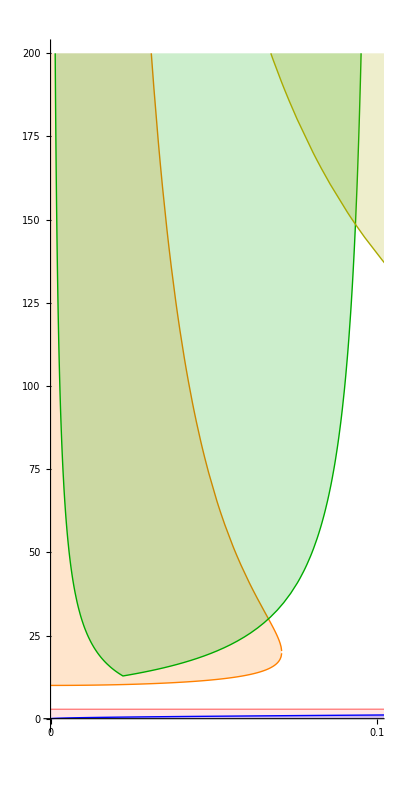
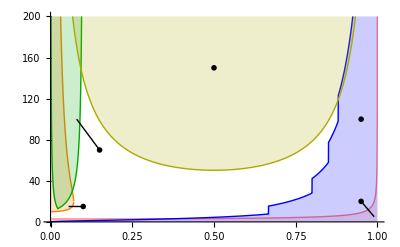
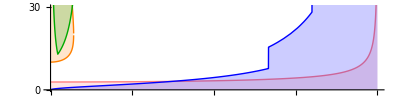
-Graphics- | -Graphics-
 | -Graphics-

```mathematica
plotrλ=Show[PlotRLI[1,0.2],PlotRLII[1,0.2], PlotRLIII[1,0.2], PlotRLIV[1,0.2], PlotRLV[1,0.2],AxesLabel->MaTeX[{"r","\\lambda"}]
];
plotrλlet=Show[plotrλ, Epilog->{Inset[MaTeX["\\mathrm{R}\\Lambda_\\mathrm{V}"],{0.5,150}],Inset[MaTeX["\\mathrm{R}\\Lambda_\\mathrm{II}"],{0.95,100}],Inset[MaTeX["\\mathrm{R}\\Lambda_\\mathrm{I}"],{0.95,20},Scaled[{0.5,0}]],Inset[MaTeX["\\mathrm{R}\\Lambda_\\mathrm{IV}"],{0.15,70},Scaled[{0.5,1}]],
Inset[MaTeX["\\mathrm{R}\\Lambda_\\mathrm{III}"],{0.1,15},Scaled[{0,0.5}]],
{Thin,Black,Line[{{0.95,20},{0.99,5}}],Line[{{0.15,70},{0.08,100}}],Line[{{0.1,15},{0.055,15}}]}}, ImageSize->400, ImagePadding->{{20,20},{20,20}}];
(* ImageDimensions[plotrλlet] *)
plotrλx=Show[plotrλ, PlotRange->{Full, {0,30}}, AspectRatio->1/4,Ticks->{Automatic, {0,15,30}},ImagePadding->{{20,20},{20,20}}, ImageSize->400];
plotrλy=Show[plotrλ, PlotRange->{{0,0.1}, {0,Ulim}}, AspectRatio->2,ImageSize->{Automatic,525/2},Ticks->{{0,0.1}, Automatic},ImagePadding->{{20,20},{20,20}}];
plotrλgr1=Grid[{{plotrλy,plotrλlet}, {,plotrλx}},Dividers->Center]
```

```mathematica
Export[SaveDir<>"figRLgrid.pdf", plotrλgr1];
```

Figure 2

```mathematica
Ulim = 160;
```

```mathematica
PlotLMI[co_,fo_]:=Plot[{Subscript[ζ, I][λ],λ}, {λ,0,Ulim}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[1]]],{Thick, Black}},PlotRange->{{0,Ulim}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[1]]]}}];
PlotLMII[co_,fo_]:=Plot[{Subscript[ζ, II][λ],λ}, {λ,0,Ulim}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[2]]],None},PlotRange->{{0,Ulim}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[2]]]}}];
PlotLMIII[co_,fo_]:=Plot[Subscript[ζ, III][λ], {λ,10,Ulim}, PlotStyle->Directive[Thick,Opacity[co],clrs[[3]]],PlotRange->{{0,Ulim}, {0,Ulim}},Exclusions->None,Filling->{1->{Axis, Directive[Opacity[fo],clrs[[3]]]}}];
PlotLMIV[co_,fo_]:=Plot[{Subscript[ζ, IV,minus][λ],Subscript[ζ, IV,plus][λ]}, {λ,578/45,Ulim}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[4]]]},PlotRange->{{0,Ulim}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[4]]]}}];
PlotLMV[co_,fo_]:=Plot[{Subscript[ζ, V,minus][λ],Subscript[ζ, V,plus][λ]}, {λ,16Pi,Ulim}, PlotStyle->{Directive[Thick,Opacity[co],clrs[[5]]]},PlotRange->{{0,Ulim}, {0,Ulim}},Exclusions->None,Filling->{2->{{1}, Directive[Opacity[fo],clrs[[5]]]}}];
```

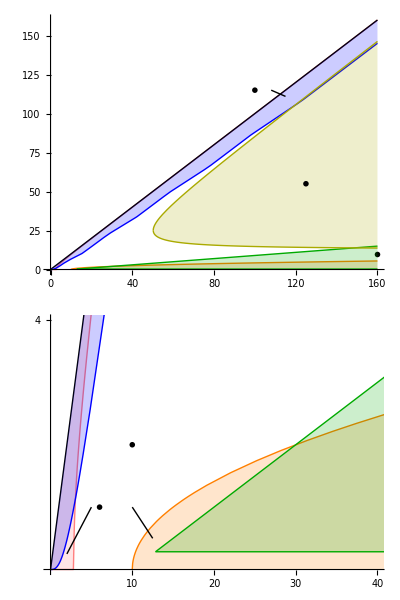

```mathematica
plotλμ=Show[PlotLMI[1,0.2],PlotLMII[1,0.2], PlotLMIII[1,0.2], PlotLMIV[1,0.2], PlotLMV[1,0.2],AxesLabel->MaTeX[{"\\lambda","\\mu"}]];
plotλμ1=Show[plotλμ, PlotRangeClipping->False,Epilog->{
Inset[MaTeX["\\Lambda\\mathrm{M}_\\mathrm{V}"],{125,55}],
Inset[MaTeX["\\Lambda\\mathrm{M}_\\mathrm{II}"],{100,115}],
Inset[MaTeX["\\Lambda\\mathrm{M}_\\mathrm{IV}"],{160,10},Scaled[{1,0.5}]],
Line[{{108,115},{115,111}}]}, ImageSize->400, ImagePadding->{{20,20},{20,20}}];
plotλμb=Show[plotλμ,PlotRange->{{0,40},{0,4}},AspectRatio->1/10, Ticks->{10Range[4],{4}},Epilog->{Thin, Inset[MaTeX["\\Lambda\\mathrm{M}_\\mathrm{III}"],{10,2}],
Inset[MaTeX["\\Lambda\\mathrm{M}_\\mathrm{I}"],{6,1}],Line[{{10,1},{12.5,0.5}}],Line[{{5,1},{2,0.25}}]}, ImageSize->400, ImagePadding->{{20,20},{20,20}}];
plotλμgr1=Grid[{{plotλμ1}, {plotλμb}},Dividers->Center]
```

```mathematica
Export[SaveDir<>"figLMgrid.pdf", plotλμgr1];
```

## §8. A computer-assisted gap filling algorithm

Figure 7

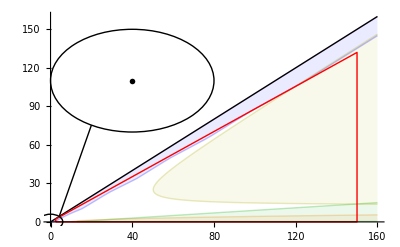

```mathematica
plotλμ2=Show[
PlotLMI[0.25,0.08],PlotLMII[0.25,0.08], PlotLMIII[0.25,0.08], PlotLMIV[0.25,0.08], PlotLMV[0.25,0.08],
Graphics[{Thick, Red,Line[{{5/2,0},{150,0},{150,22/25 150},{5/2,22/25 5/2},{5/2,0}}]}],
PlotRange->{{0,Ulim},{0,Ulim}},AxesLabel->MaTeX[{"\\lambda", "\\mu"}]
];
plotλμ3=plotλμ1=Show[plotλμ2, PlotRangeClipping->False,Epilog->{Thin,Circle[{0,0},6],Circle[{40,110},40], Line[{{40,110}-40{Cos[Pi/3],Sin[Pi/3]},6{1,1}/Sqrt[2]}],Inset[Show[plotλμ2,PlotRange->{{0,6},{0,6}},AxesLabel->None, Ticks->{{{5,MaTeX["5"]}},{{5,MaTeX["5"]}}},ImageSize->100],{40,110}]
}]
```

```mathematica
Export[SaveDir<>"figLMcomp.pdf", plotλμ3];
```

Figure 8

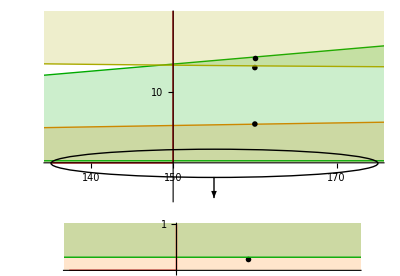

```mathematica
Ulim=180;
plotthm81c1=GraphicsColumn[{plotthm81c11=Show[
PlotLMI[1,0.2],PlotLMII[1,0.2], PlotLMIII[1,0.2], PlotLMIV[1,0.2], PlotLMV[1,0.2],
Graphics[{Thick, Red,Line[{{135,0},{150,0},{150,22/25 150}}], Thin,Black, Circle[{155,0},{20,2}]}],
PlotRange->{{135,175},{-5,21}},AxesLabel->MaTeX[{"\\lambda", "\\mu"}],AxesOrigin->{150,0}, AspectRatio->1/2, Ticks->{{140, 150, 170}, {10}}, 
(*PlotRangePadding->{{0, 0},{5, 2}},*) Epilog->{Thin,Arrowheads[0.02], Arrow[{{155,-2}, {155,-5}}],
Inset[MaTeX["\\mu=\\zeta_{\\mathrm{III}}(\\lambda)"],{160,5.5},Scaled[{0.5,0}]],Inset[MaTeX["\\mu=\\zeta_{\\mathrm{V},-}(\\lambda)"],{160,13.5},Scaled[{0.5,1}]],Inset[MaTeX["\\mu=\\zeta_{\\mathrm{IV},+}(\\lambda)"],{160,14.9},Scaled[{0.5,0}],Automatic,{1,1/10}]},
ImagePadding->{{0,15},{8,20}},
ImageSize->400],
plotthm81c12=Show[
PlotLMI[1,0.2],PlotLMIII[1,0.2], PlotLMIV[1,0.2],
Graphics[{Thick, Red,Line[{{135,0},{150,0},{150,1}}]}],
PlotRange->{{135,175},{0,1}}, AspectRatio->1/10,AxesOrigin->{150,0},AxesLabel->{MaTeX["\\phantom{\\lambda}"],None}, Ticks->{{150},{1}},(*PlotRangePadding->{{0,0},{0,0.5}},*)
Epilog->{Inset[MaTeX["\\mu=\\zeta_{\\mathrm{IV},-}(\\lambda)"],{160,0.25},Scaled[{0.5,0}]]},ImagePadding->{{0,15},{20,2}},ImageSize->350
]},Spacings->0, Frame->None, ImageSize->{UpTo[400], Full}, Alignment->Center]
```

```mathematica
Export[SaveDir<>"plotthm81c1.pdf",plotthm81c1];
```

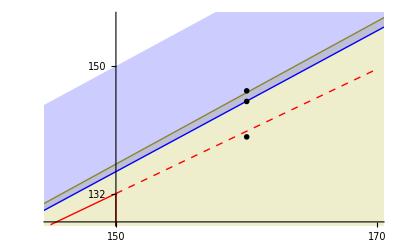

```mathematica
Ulim=180; plotthm81c2=Show[PlotLMV[1,0.2],PlotLMII[1,0.2],
Graphics[{Thick, Red,Line[{{150,0},{150,22/25 150},{145,22/25 145}}],Dashed, Line[{{150,22/25 150},{170,22/25 170}}]}],
PlotRange->{{145,170}, {128,157}},AxesOrigin->{150,128},Ticks->{{150,170}, {150 22/25,150}},AxesLabel->MaTeX[{"\\lambda", "\\mu"}],Epilog->{Inset[MaTeX["\\mu=\\zeta_{\\mathrm{V},+}(\\lambda)"],{160,146.5},Scaled[{0.5,0}],Automatic,{1,1/2}],Inset[MaTeX["\\mu=\\zeta_{\\mathrm{II}}(\\lambda)"],{160,145},Scaled[{0.5,1}],Automatic,{1,1/2}],
Inset[MaTeX["\\mu=\\zeta_{\\mathrm{comp}}(\\lambda)"],{160,140},Scaled[{0.5,1}],Automatic,{1,1/2}]},ImageSize->400]
```

```mathematica
Export[SaveDir<>"plotthm81c2.pdf",plotthm81c2];
```

Proof of Theorem 8.1

Case 2

```mathematica
Simplify[Subscript[η, II][r]/Subscript[η, V][r], 1>r>22/25]
(%/.r->22/25)^2
Sqrt[%]//N
```

(5 r^(3/2))/4

1331/1250

1.03189

Case 3

```mathematica
FullSimplify[Subscript[ζ, IV,plus][λ]/Subscript[ζ, V,minus][λ], λ>16Pi]
```

(10-λ)/(-5 λ+5 √(λ (-16 π+λ)))

```mathematica
((λ-10)(5 λ+5 √(λ (-16 π+λ)))//Simplify)/((5 λ-5 √(λ (-16 π+λ)))(5 λ+5 √(λ (-16 π+λ)))//Simplify)
%/.λ->150//Simplify
%//N
```

((-10+λ) (5 λ+5 √(λ (-16 π+λ))))/(400 π λ)

(7 (15+√(3 (75-8 π))))/(60 π)

1.01126

```mathematica
FullSimplify[Subscript[ζ, V,plus][λ]/Subscript[ζ, IV,plus][λ], λ>150]
```

(5 λ+5 √(λ (-16 π+λ)))/(-10+λ)

```mathematica
FullSimplify[Subscript[ζ, IV,plus][λ]/Subscript[ζ, III][λ]]
%/.λ->150//Simplify
%//N
FullSimplify[Subscript[ζ, III][λ]/Subscript[ζ, IV,minus][λ]]
%/.λ->150//Simplify
%//N
```

1/2 √(-2+λ/5)

√7

2.64575

225/64 √(-2+λ/5)

(225 √7)/32

18.6029

```mathematica
FullSimplify[Subscript[ζ, II][λ]/(22/25λ),λ>150]
FullSimplify[Subscript[ζ, V,plus][λ]/(22/25λ),λ>150]
```

(25 (25 π^2+2 λ^2-5 π √(25 π^2+4 λ^2)))/(44 λ^2)

(25 (λ+√(λ (-16 π+λ))))/(44 λ)

```mathematica
(25 (2 -5 π √(25 π^2 λ^-4+4 λ^-2)))/44/.λ->150//Simplify
%//N
```

25/22-(π √(3600+π^2))/1584

1.0172

```mathematica
(25 (λ+√(λ (-16 π+λ))))/(44 λ)
FullSimplify[%/.λ->150]
%//N
```

(25 (λ+√(λ (-16 π+λ))))/(44 λ)

5/132 (15+√(3 (75-8 π)))

1.03148

Figure 9

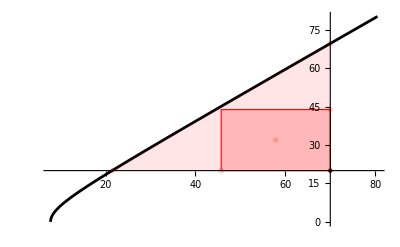

```mathematica
l0= 70; m0= 20; P0= 15;
l0max = Sqrt[m0^2+4P0];
m0max=Sqrt[l0^2-4P0];
l1 = 1/2 l0max +1/2 l0;
m1=0.95Sqrt[l1^2-4P0]+0.05m0;
fighyperb=Show[Plot[Sqrt[λ^2-4P0], {λ,2Sqrt[P0],1.15l0}, AxesOrigin->{l0,m0}, Ticks->None,PlotStyle->Black], Plot[Sqrt[λ^2-4P0], {λ,l0max,l0},PlotStyle->None, Filling->{1->{Axis, Directive[Opacity[0.1],Red]}}],
Epilog->{
Black,PointSize[Medium],Point[{l0,m0}],
EdgeForm[Red],Directive[Opacity[0.2],Red],Rectangle[{l1,m0},{l0,m1}],
Inset[MaTeX["\\lambda_1"],{l1,m0},{Center,Top}],
Inset[MaTeX["\\mu_1"],{l0,m1},{Left,Center}],
Inset[MaTeX["\\mathrm{M}(\\lambda_0,p_0)"],{l0,m0max},{Left,Top}],
Inset[MaTeX["\\Lambda(\\mu_0,p_0)"],{l0max,m0},{Left,Top}],
Inset[MaTeX["(\\lambda_0,\\mu_0)"],{l0,m0},{Left,Top}],
Inset[MaTeX["\\mathfrak{R}(\\lambda_0,\\mu_0,p_0;\\alpha,\\beta)"],{l1+l0,m1+m0}/2]
}
]
```

```mathematica
Export[SaveDir<>"fighyperb.pdf", fighyperb];
```

Figure 10

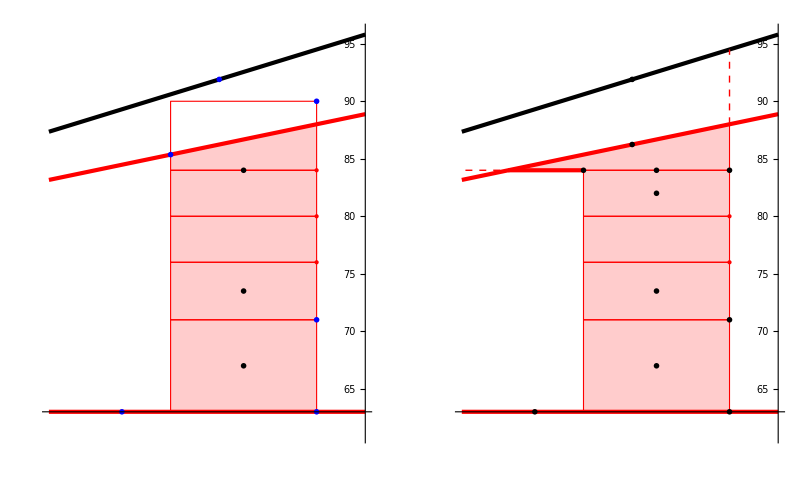

```mathematica
μfiction=(* 1.02λ - 7.5 *)1.3λ - 35.5; μ0fiction = 63; λ0=100; λ1= 97;
μsfig1={63, 71, 76, 80, 84, 90}; 
colfig11=Plot[{μ0fiction,22/25 λ, μfiction}, {λ,λ1-2.5,λ0+1}, PlotStyle->{{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black}}, PlotRange->{{61,96}},AspectRatio->5/4, Epilog->{{EdgeForm[Red],Directive[Opacity[0.2],Red],Table[Rectangle[{λ1,μsfig1[[jj]]},{λ0,μsfig1[[jj+1]]}],{jj,1,4}],
Polygon[{{λ0, μsfig1[[5]]}, {λ0, 22/25 λ0}, {λ1, 22/25 λ1}, {λ1,  μsfig1[[5]]}}]},
{EdgeForm[{Red, Dashed}],Directive[Opacity[0],Red],Polygon[{ {λ0, 22/25 λ0},{λ0, μsfig1[[6]]}, {λ1,  μsfig1[[6]]},{λ1, 22/25 λ1}}]},
Inset[MaTeX["\\mathfrak{R}^{(k,0)}"],{98.5,1/2(μsfig1[[1]]+μsfig1[[2]])}],
Inset[MaTeX["\\mathfrak{R}^{(k,1)}"],{98.5,1/2(μsfig1[[2]]+μsfig1[[3]])}],
Inset[MaTeX["\\mathfrak{R}^{\\left(k,X_k-1\\right)}"],{98.5,μsfig1[[5]]}, Scaled[{1/2,-0.1}]],
PointSize[Large], Red,
Point[Table[{100, μsfig1[[jj]]},{jj,1,5}]],Blue,Point[{100,μsfig1[[6]] }],
Inset[MaTeX["\\mu^{(k,0)}"],{100,μsfig1[[1]]},Scaled[{-0.1,0}]],
Inset[MaTeX["\\mu^{(k,1)}"],{100,μsfig1[[2]]},Scaled[{-0.1,0}]],
Inset[MaTeX["\\mu^{\\left(k,X_k\\right)}"],{100,μsfig1[[6]]},Scaled[{-0.1,0}]],
Inset[MaTeX["\\mu=\\zeta_\\mathrm{comp}^{(k+1)}(\\lambda)=\\zeta_\\mathrm{comp}^{(k)}(\\lambda)"], {97,22/25 97},Scaled[{-0.05,-0.1}],Automatic,{1,1/5}],
Inset[MaTeX["\\mu=\\lambda"], {98,μfiction/.λ->98},Scaled[{-0.2,1.1}],Automatic,{1,1/4}],
Inset[MaTeX["\\mu=0"], {96,63},Scaled[{0.5,-0.1}]]
},
AxesOrigin->{101,63}, AxesLabel->MaTeX[{"\\lambda","\\mu"}], 
Ticks->{{{97, MaTeX["\\lambda^{(k+1)}"]},{100, MaTeX["\\lambda^{(k)}"]}},None}
] ;
colfig12=Plot[{μ0fiction,22/25 λ, μfiction}, {λ,λ1-2.5,λ0+1}, PlotStyle->{{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black}}, PlotRange->{{61,96}},AspectRatio->5/4, Epilog->{{EdgeForm[Red],Directive[Opacity[0.2],Red],Table[Rectangle[{97,μsfig1[[jj]]},{100,μsfig1[[jj+1]]}],{jj,1,4}],
Triangle[{{100,μsfig1[[5]] }, {100,22/25 100 }, {μsfig1[[5]] 25/22, μsfig1[[5]]}}]},
{Red, Dashed, Line[{{100,22/25 100 },{100,102-7.5}}],Line[{{97,μsfig1[[5]]},{λ1-2.5,μsfig1[[5]]}}]},
Inset[MaTeX["\\mathfrak{R}^{(k,0)}"],{(λ0+λ1)/2,1/2(μsfig1[[1]]+μsfig1[[2]])}],
Inset[MaTeX["\\mathfrak{R}^{(k,1)}"],{(λ0+λ1)/2,1/2(μsfig1[[2]]+μsfig1[[3]])}],
Inset[MaTeX["\\mathfrak{R}^{\\left(k,X_k-1\\right)}"],{(λ0+λ1)/2,1/2(μsfig1[[4]]+μsfig1[[5]])}],
Inset[MaTeX["\\mathfrak{T}^{\\left(k,X_k\\right)}"],{(λ0+λ1)/2,μsfig1[[5]]},Scaled[{1/2,-0.1}]],
Red,AbsoluteThickness[3],Line[{{μsfig1[[5]] 25/22, μsfig1[[5]]},{λ1,μsfig1[[5]]}}],
PointSize[Large], Red,
Point[Table[{λ0, μsfig1[[jj]]},{jj,1,4}]],Black,Point[{λ0,μsfig1[[5]] }],
Inset[MaTeX["\\mu^{(k,0)}"],{λ0,μsfig1[[1]]},Scaled[{-0.1,0}]],
Inset[MaTeX["\\mu^{(k,1)}"],{λ0,μsfig1[[2]]},Scaled[{-0.1,0}]],
Inset[MaTeX["\\mu^{\\left(k,X_k\\right)}"],{λ0,μsfig1[[5]]},Scaled[{-0.1,0}]],
Inset[MaTeX["\\mu=\\zeta_\\mathrm{comp}^{(k)}(\\lambda)"], {98,22/25 98},Scaled[{-0.2,-0.1}],Automatic,{1,1/5}],
Inset[MaTeX["\\mu=\\zeta_\\mathrm{comp}^{(k+1)}(\\lambda)"], {97,μsfig1[[5]]},Scaled[{1.1,1.13}]],
Inset[MaTeX["\\mu=\\lambda"], {98,μfiction/.λ->98},Scaled[{-0.2,1.1}],Automatic,{1,1/4}],
Inset[MaTeX["\\mu=0"], {96,63},Scaled[{0.5,-0.1}]]
},
AxesOrigin->{101,63}, AxesLabel->MaTeX[{"\\lambda","\\mu"}], 
Ticks->{{{97, MaTeX["\\lambda^{(k+1)}"]},{100, MaTeX["\\lambda^{(k)}"]}},None}
];
figcolfig=GraphicsGrid[{{colfig11, colfig12}}]
```

```mathematica
Export[SaveDir<>"figcol.pdf", figcolfig];
```

Verified rational approximations routines

```mathematica
CosUp[x_]:=1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600;
CosDown[x_]:=1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+x^12/479001600-x^14/87178291200;
VerifiedQUpArcCos[x_,ϵ_]:=Module[{ac0,ac},
ac0=ArcCos[x];
If[MatchQ[ac0,_Rational]|| IntegerQ[ac0], ac=ac0, 
 ac=Rationalize[ac0+2ϵ,ϵ];If[CosUp[ac]>=x, Message[VerifiedQUpArcCos::Error, x], ac]]; 
(* ac=Rationalize[ArcCos[x]+2ϵ,ϵ]; *)
ac
];
VerifiedQUpArcCos::Error="ArcCosUp of argument `1` is wrong!";
VerifiedQDownArcCos[x_,ϵ_]:=Module[{ac0, ac},
 ac0=ArcCos[x];
If[MatchQ[ac0,_Rational]|| IntegerQ[ac0], ac=ac0, 
 ac=Rationalize[ac0-2ϵ,ϵ];
If[CosDown[ac]<=x, Message[VerifiedQDownArcCos::Error, x], ac]];
ac
];
VerifiedQDownArcCos::Error="ArcCosDown of argument `1` is wrong!";
VerifiedQUpSqrt[x_,ϵ_]:=Module[{ac0, ac},
ac0=Sqrt[x];
If[MatchQ[ac0,_Rational]|| IntegerQ[ac0], ac=ac0, 
 ac=Rationalize[ac0+2ϵ,ϵ];  If[ac^2<x, Message[VerifiedQUpSqrt::Error, x], ac]];
ac
];
VerifiedQUpSqrt::Error="SqrtUp of argument `1` is wrong!";
VerifiedQDownSqrt[x_,ϵ_]:=Module[{ac0, ac},
 ac0=Sqrt[x];
If[MatchQ[ac0,_Rational]|| IntegerQ[ac0], ac=ac0, 
 ac=Rationalize[ac0-2ϵ,ϵ];  If[ac^2>x, Message[VerifiedQDownSqrt::Error, x], ac]];
ac
];
VerifiedQDownSqrt::Error="SqrtDown of argument `1` is wrong!";
VerifiedQUpRoot[x_,d_,ϵ_]:=Module[{ac0, ac},
ac0=x^(1/d);
If[MatchQ[ac0,_Rational]|| IntegerQ[ac0], ac=ac0, 
 ac=Rationalize[ac0+2ϵ,ϵ];  If[ac^d<x, Message[VerifiedQUpRoot::Error, x], ac]];
ac
];
VerifiedQUpRoot::Error="RootUp `2` of argument `1` is wrong!";
VerifiedQDownRoot[x_,d_,ϵ_]:=Module[{ac0, ac},
 ac0=x^(1/d);
If[MatchQ[ac0,_Rational]|| IntegerQ[ac0], ac=ac0, 
 ac=Rationalize[ac0-2ϵ,ϵ];  If[ac^d>x, Message[VerifiedQDownRoot::Error, x], ac]];
ac
];
VerifiedQDownSqrt::Error="RootDown `2` of argument `1` is wrong!";
PiUp[ϵ_]:=3VerifiedQUpArcCos[1/2,ϵ];
PiDown[ϵ_]:=3VerifiedQDownArcCos[1/2,ϵ];
```

Verified setting-up

```mathematica
ϵ0=10^(-4);
PiD=PiDown[ϵ0]
PiU =PiUp[ϵ0]
```

267/85

531/169

```mathematica
GQDown[λ_, z_, ϵ_:ϵ0]:=(VerifiedQDownSqrt[λ^2-z^2, ϵ]-z VerifiedQUpArcCos[z/λ, ϵ])/PiU;
GQUp[λ_, z_, ϵ_:ϵ0]:=(VerifiedQUpSqrt[λ^2-z^2, ϵ]-z VerifiedQDownArcCos[z/λ, ϵ])/PiD;
HQUp[λ_,z_, ϵ_:ϵ0]:=(3λ^2+2z^2)/(24PiD VerifiedQDownSqrt[(λ^2-z^2)^3,ϵ]);
FQDown[λ_, z_, ϵ_:ϵ0]:=If[z<λ, Max[GQDown[λ,z, ϵ]-HQUp[λ,z, ϵ],-1/4],-1/4];
Pcount[λ_,μ_]:=Floor[G[λ,0]-F[μ,0]]+2Sum[Floor[G[λ,m]-F[μ,m]],{m,1,Floor[λ]}];
𝒫Up[λ_,μ_, ϵ_:ϵ0]:=Floor[GQUp[λ,0,ϵ]-FQDown[μ,0,ϵ]]+2Sum[Floor[GQUp[λ,m,ϵ]-FQDown[μ,m,ϵ]],{m,1,Floor[λ]}];
```

```mathematica
Λmax[μ0_, p0_, ϵ_:ϵ0]:= VerifiedQUpSqrt[μ0^2+4p0, ϵ];
Μmax[λ_, p0_, ϵ_:ϵ0]:= VerifiedQDownSqrt[λ^2-4p0, ϵ];
```

```mathematica
ζcompmax=150 22/25;
```

```mathematica
OneBlock[λ0_, μ0_,λ1_, α_, ϵ_:ϵ0]:=Module[{p0,λ1new, λ1newtemp, μ1, flag,δ0},
If[μ0>Min[ζcompmax ,22/25 λ0],  Return[{λ0,μ0,None,λ1, λ1,None,2}]];
p0=𝒫Up[λ0,μ0, ϵ];
δ0=(λ0^2-μ0^2)/4-p0;
If[δ0<=0, Print["negative difference!!"]; Return[{λ0,μ0,p0,None, None,None,-1}]];
If[p0==0, ζcompmax= μ0; Return[{λ0,μ0,p0,λ1, λ1,None,0}]];
 λ1newtemp= VerifiedQUpRoot[1.(α Λmax[μ0, p0, ϵ] + (1-α) λ0),1,ϵ];
λ1new=Max[λ1newtemp ,λ1];
μ1 = VerifiedQUpRoot[1.(99/100 Μmax[λ1new, p0, ϵ]+1/100 μ0),1,ϵ];
{λ0,μ0,p0, λ1newtemp,λ1new,μ1,1}
];
```

```mathematica
BlockColumn1[λ0_,μ0_, α_, ϵ_:ϵ0] :=Module[{p,λ1,λ1new, μ1, columndata, oneblock,columnsummary, ζwrite},
μ1=μ0;
ζwrite=Min[ζcompmax ,22/25 λ0];
temp=PrintTemporary[ProgressIndicator[Dynamic[μ1], {μ0,ζwrite}],"μ"];
oneblock=OneBlock[λ0,μ0,0,α, ϵ];
columndata={oneblock};
While[oneblock[[7]]==1,
 μ1=oneblock[[6]];
λ1new=oneblock[[5]];
oneblock=OneBlock[λ0, μ1,λ1new,α,  ϵ];
AppendTo[columndata,oneblock];
];
columnsummary={λ0, ζwrite,Length[columndata], Last[columndata][[7]]};
NotebookDelete[temp];
{columndata, columnsummary}
]
```

```mathematica
ManyColumns[λstart_, μstart_, α_, λend_, ϵ_:ϵ0]:=Module[{timethis, columndata, columnsummary,alldata, allsummaries,totaltime, totalcount, λ1},
totaltime=0;
totalcount=0;
λ1=λstart;
alldata={};
allsummaries={};
temp1=PrintTemporary[ProgressIndicator[Dynamic[λ1], {λstart,λend}],"λ"];
While[λ1>λend,
{timethis, {columndata,columnsummary}}= Timing[BlockColumn1[λ1, μstart, α]];
totaltime = totaltime+timethis;
totalcount=totalcount+Length[columndata]-If[(columndata//Last)[[7]]==2,1,0];
AppendTo[alldata, columndata];
AppendTo[allsummaries, columnsummary];
λ1 = (columndata//Last)[[5]];
NotebookDelete[temp2];
temp2=PrintTemporary["λ = ",λ1, " ≈ ", N[λ1],  "; total time = ",totaltime, "; total count = ", totalcount, "; ζcompmax = " ,columnsummary[[2]]," ≈ ", N[columnsummary[[2]]]];
If[ζcompmax==0, Break[]];
];
{alldata,allsummaries,totaltime,totalcount}
];
```

Actual computations

```mathematica
(* ζcompmax=150 22/25; 
(* α = 9/10 *)
{alldata,allsummaries,totaltime,totalcount}=ManyColumns[150,0,9/10,5/2];
{totaltime,totalcount}
alldata//Last//Last
Length[alldata] *)
```

```mathematica
(*ζcompmax=150 22/25; 
(* α = 3/4 *)
{alldata,allsummaries,totaltime,totalcount}=ManyColumns[150,0,3/4,5/2];
{totaltime,totalcount}
alldata//Last//Last
Length[alldata]*)
```

```mathematica
ζcompmax=150 22/25; 
(* α = 2/3 *)
{alldata,allsummaries,totaltime,totalcount}=ManyColumns[150,0,2/3,5/2];
{totaltime,totalcount}
alldata//Last//Last
Length[alldata]
```

{116.594,8473}

{265/104,71/82,0,179/82,179/82,None,0}

227

```mathematica
Save[SaveDir<>"alldata.wl",alldata]
```

```mathematica
alldataflat=Flatten[alldata,1];
```

Figure 11

```mathematica
zeropoints=Table[po[[1;;2]], {po,Select[alldataflat, #[[7]]==0&]}];
abovepoints=Table[po[[1;;2]], {po,Select[alldataflat, #[[7]]==2&]}];
normalpoints=Table[po[[1;;2]], {po,Select[alldataflat, #[[7]]==1&]}];
```

```mathematica
zp=zeropoints//Reverse;
tz=Table[{zp[[j]][[2]],x<=zp[[j]][[1]]}, {j,1,Length[zp]}];
tz=Join[{{0,x<=5/2}},tz];
```

```mathematica
pr=30;figcalcend=Show[Graphics[{PointSize[Medium],{Black,Line[{{0,0},{pr,pr}}]},{Red,Inset[Style["×", Large],{179/82,0},{Center,Center}]},{Directive[Opacity[0.25],Red],Point[Select[normalpoints, #[[1]]<=pr &]]}, {Darker[Blue], Point[Select[abovepoints, #[[1]]<=pr &]]}, {Black,Point[Select[zp, #[[1]]<=pr &]]}},Axes->True,AxesOrigin->{0,0},PlotRange->{{0,pr},{0,pr}}],
Plot[Min[Piecewise[tz,22/25 x],22/25 x],{x,5/2-0.001,pr},Exclusions->None, PlotStyle->Red, PlotPoints->400], AxesLabel->MaTeX[{"\\lambda","\\mu"}]]
```

-Graphics-

```mathematica
Export[SaveDir<>"figcalcend.pdf", figcalcend];
```

Figure 12

```mathematica
tix={50,100,150};tiy={0.25,0.5,0.75};figdlambda=ListLinePlot[Table[{alldata[[k]][[1]][[1]], alldata[[k]][[1]][[1]]-alldata[[k+1]][[1]][[1]]}, {k,1,226}], AxesOrigin->{0,0.2},AxesLabel->MaTeX[{"\\lambda^{(k)}","\\lambda^{(k)}-\\lambda^{(k+1)}"}],PlotStyle->{AbsoluteThickness[1],Red},Epilog->{Red, Arrow[{{140,0.4},{100,0.4}}]}, ImageSize->280,
Ticks->{{tix, MaTeX[tix]}//Transpose, {tiy, MaTeX[tiy]}//Transpose}
];
```

```mathematica
ks= {1,81,161};
tix={40,80,120};tiy={3,6,9};
figdmu=ListLinePlot[
Table[
Table[{alldata[[k]][[j]][[2]], alldata[[k]][[j]][[6]]-alldata[[k]][[j]][[2]]}, {j,1,Length[alldata[[k]]]-1}],{k,ks}],
PlotRange->All, AxesLabel->MaTeX[{"\\mu^{(k,j)}","\\mu^{(k,j+1)}-\\mu^{(k,j)}"}],PlotLegends->Placed[Table[MaTeX["k="<>ToString[k-1]<>",\\ \\lambda^{("<>ToString[k-1]<>")}="<>ToString[TeXForm[alldata[[k]][[1]][[1]]]]],{k,ks}],{Right,Top}],PlotStyle->AbsoluteThickness[1],Epilog->{Black, Arrow[{{25,0.5},{60,0.5}}]}, ImageSize->280,Ticks->{{tix, MaTeX[tix]}//Transpose, {tiy, MaTeX[tiy]}//Transpose}];
```

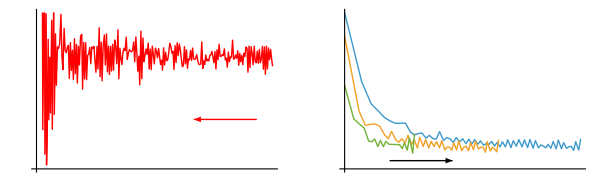

```mathematica
figdlambdamu=GraphicsRow[{figdlambda, figdmu}]
```

```mathematica
Export[SaveDir<>"figdlambdamu.pdf", figdlambdamu];
```

Exporting data for web

```mathematica
FNum[n_, ℓ_]:=StringPadRight[ToString[InputForm[n]],ℓ];
FStr[s_, ℓ_]:=StringPadRight[s,ℓ];
FDa[ℓ_]:=StringRepeat["-",ℓ];
FAllSum[kk_, sum_]:={FNum[kk-1,4], FNum[sum[[1]],16], FNum[sum[[2]],16], FNum[sum[[3]]-1,4],If[sum[[4]]==2, "above ΛM_{comp}", "zero count"]};
tallsumhead={{FStr["k",4],FStr["λ^{(k)}",16],FStr["ζ_{comp}(λ^{(k)})",16],"X_k ", "how column ends"}, {FDa[4],FDa[16],FDa[16],FDa[4],FDa[18]}};
```

```mathematica
tallsummaries=Join[tallsumhead,Table[FAllSum[kk,allsummaries[[kk]]], {kk,1,Length[allsummaries]}],{{FNum[Length[allsummaries],4],FNum[(alldata//Last//Last)[[5]],16],FStr["",16],FStr["",4], "λ^{(k)} is below 5/2"}}];
```

```mathematica
Export[SaveDir<>"columnsummary.txt",tallsummaries,"Table"];
```

```mathematica
sall = OpenWrite[SaveDir<>"allcolumns.txt",CharacterEncoding->"UTF8"];
Do[
WriteString[sall, StringRepeat["=",62], "\n"];
WriteString[sall, "COLUMN "<>FNum[kk-1,3], "\n"];
WriteString[sall, "λ^{("<>ToString[kk-1]<>")} = ", FNum[alldata[[kk,1,1]],16], "\n"];
WriteString[sall, "ζ_{comp}(λ^{("<>ToString[kk-1]<>")} = ", FNum[allsummaries[[kk,2]],16],"\n" ];
WriteString[sall,"X_k = ", FNum[allsummaries[[kk]][[3]]-1,4], "\n"];
WriteString[sall, StringRepeat["-",62], "\n"];
WriteString[sall, FStr["j",4], FStr["μ^{(j)}",16],FStr["p^{(k,j)}",12],  FStr["λ^{("<>ToString[kk]<>")}_{temp}",16], FStr["λ^{("<>ToString[kk]<>")}",16], "\n", StringRepeat["-",62], "\n"];
Do[
WriteString[sall, FNum[j-1,4], FNum[alldata[[kk,j,2]],16]]; WriteString[sall,If[NumberQ[alldata[[kk,j,3]]],FNum[alldata[[kk,j,3]],12],"above       "]];
WriteString[sall,If[NumberQ[alldata[[kk,j,3]]],FNum[alldata[[kk,j,4]],16], FStr["",16]]];
WriteString[sall,If[NumberQ[alldata[[kk,j,3]]],FNum[alldata[[kk,j,5]],16], FStr["",16]]];
WriteString[sall,"\n"];
,{j,1,Length[alldata[[kk]]]}]; 
,{kk,1,Length[alldata]}];
Close[sall];
```

## Extras

Numerically computed phase functions and their differences (in case needed; not in the paper)

```mathematica
snthetaν[ν_,X_]:=theta/.NDSolve[{theta'[x]==2/(Pi x (BesselJ[ν,x]^2 +BesselY[ν,x]^2)), theta[10^(-7)]==-Pi/2}, theta, {x,10^(-7),X}][[1]]
```

```mathematica
theta10=snthetaν[10,50];
```

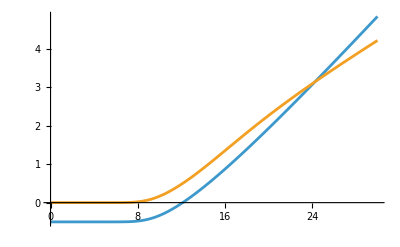

```mathematica
Plot[1/Pi{theta10[x],(theta10[x]-theta10[0.5x ])}//Evaluate,{x,10^(-7),30},PlotRange->All]
```